```mathematica
mcSim[β_,j_,n_,iter_]:=Module[{grid=Array[1&,{n,n}],x,y,r,diff,a,k,l,m,grids,mags},grids=Array[{}&,iter];
mags=Array[{}&,iter];
If[j≥0,
m=n^2;
,
m=1/4*((-1)^n-1)^2 ;
];
For[k=1,k≤iter,k++,
For[l=1,l≤n^2,l++,               (*sweep*)
x=RandomInteger[{1,n}];y=RandomInteger[{1,n}];diff=2*j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
a=If[diff>0,Exp[-β*diff],1];
r=RandomReal[];
If[a>r,
grid[[x,y]]=-grid[[x,y]];
If[j≥0,
m=m+2*grid[[x,y]];
,
m=m+2*(-1)^(x+y)*grid[[x,y]];
];
];
];
grids[[k]]=grid;
mags[[k]]=m;
];
(*Print[rejected];*)
{mags,grids}
]
magnetization[grids_]:=1/(Dimensions[grids[[1]]][[1]]^2*Dimensions[grids][[1]])*Total[Flatten[grids]]
magnetizationSq[grids_]:=1/(Dimensions[grids][[1]])*Total[Flatten[Table[(1/Dimensions[grids[[1]]][[1]]^2*Total[Flatten[grids[[i]]]])^2,{i,1,Dimensions[grids][[1]]}]]]
suscept[mag_,magSq_,β_]:=β*(magSq-mag^2)
energy[grids_,j_]:=Module[{grid,n,x,y,i},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum=sum-j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
];
];
];
sum/(2*Dimensions[grids][[1]])   (*   faktor 1/2: jedes paar wird sonst doppelt gezählt*)
]
energySq[grids_,j_]:=Module[{grid,n,sum1,x,y,i},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
sum1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum1=sum1-(j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]));
];
];
sum = sum + sum1^2/4;
];
sum/Dimensions[grids][[1]]
]
specificHeat[energy_,energySq_,β_]:=β^2*(energySq-energy^2)
magAntiferro[grids_]:=Module[{grid,n,i,x,y},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m=m+(-1)^(x+y)*grid[[x,y]];
];
];
];
m/(Dimensions[grids][[1]]*n^2)
]
magAntiferroSq[grids_]:=Module[{grid,n,m1,i},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
m1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m1=m1+(-1)^(x+y)*grid[[x,y]];
];
];
m=m+m1^2/n^2;
];
m/Dimensions[grids][[1]]
]
```

```mathematica
n=20;j=-1;steps=1000;β=0.441;
s=mcSim[β,j,n,steps];
m=Total[s[[1]]]/(Dimensions[s[[1]]][[1]]*n^2)
t=#^2&/@s[[1]];
msq=Total[t]/(Dimensions[t][[1]]*n^2)
magAntiferro[s[[2]]]
magAntiferroSq[s[[2]]]
```

69043/100000

10395361/50000

69043/100000

10395361/50000

```mathematica
n=4;j=1;steps=1000;β=0.5;
s=mcSim[β,j,n,steps];
Total[s[[1]]]/(Dimensions[s[[1]]][[1]]*n^2)
magnetization[s[[2]]]
```

2671/8000

2671/8000

```mathematica
s[[1]]
s[[2,1]]//MatrixForm
```

{4}

(-1 | -1 | 1 | -1
1 | 1 | -1 | -1
1 | 1 | 1 | 1
1 | -1 | 1 | 1)

```mathematica
Dimensions[s]
```

{2,1}

```mathematica
Total[s[[1]]]/(Dimensions[s][[1]]*n^2)
```

1/8

```mathematica
test[x_]:=Module[{y},
y=x+1;
{x^2,y}]
```

```mathematica
test[4]
```

{16,5}

```mathematica
n=4;j=1;steps=1000;
βs=Table[β,{β,0.2,0.7,0.05}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,201;;-1]];
ms=Parallelize[Table[magAntiferro[simβvar[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
Print["p1"]
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
```

4.6201

p1

18.52404

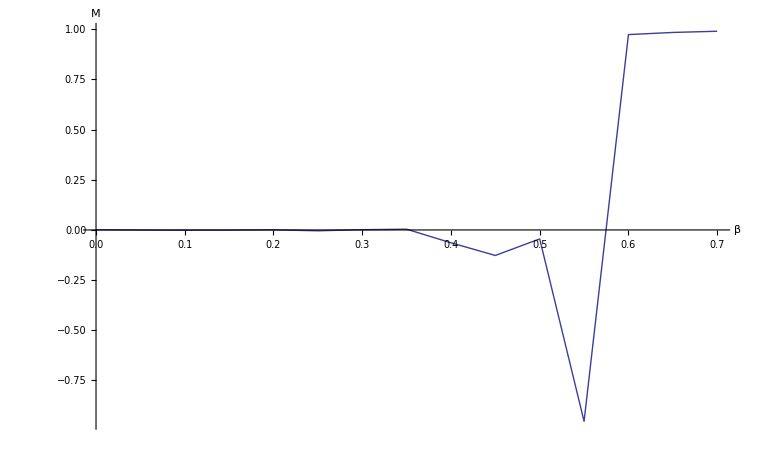

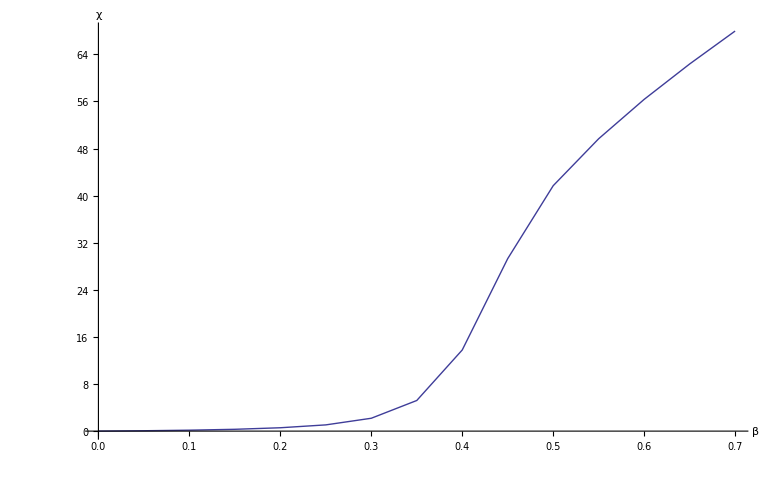

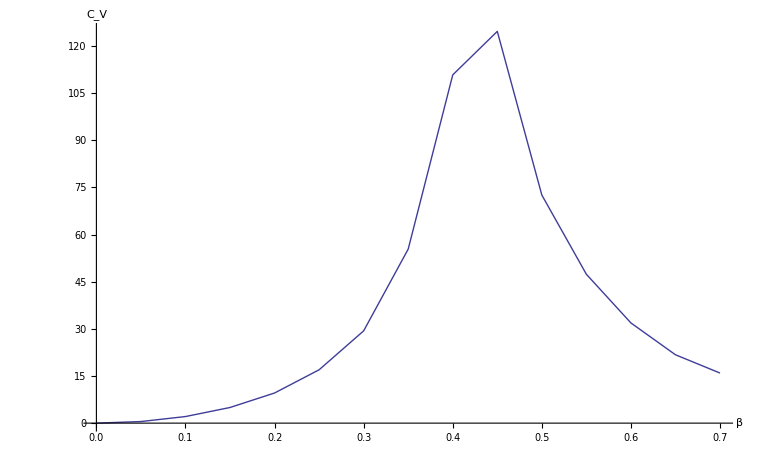

```mathematica
n=4;j=-1;steps=10000;
βs=Table[β,{β,0.2,0.7,0.05}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,2001;;-1]];
ms=Parallelize[Table[magAntiferro[simβvar[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
Print["p1"]
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p1,PlotRange->All]*)
suscepts=Parallelize[Table[suscept[ms[[i]],magAntiferroSq[simβvar[[i]]],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
Print["p2"]
p2=Table[{βs[[i]],suscepts[[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p2,PlotRange->All]*)
heats=AbsoluteTiming[Parallelize[Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}]]];
heats[[1]]
Print["p3"]
p3=Table[{βs[[i]],heats[[2]][[i]]},{i,1,Dimensions[βs][[1]]}];
(*ListLinePlot[p3,PlotRange->All]*)
ListLinePlot[p1,PlotRange->All,AxesLabel->{β,M}]
ListLinePlot[p2,PlotRange->All,AxesLabel->{β,χ}]
ListLinePlot[p3,PlotRange->All,AxesLabel->{β,Subscript[C, V]}]
```

```mathematica
n=20;j=1;steps=100000;
βs=Table[β,{β,0.0,0.7,0.05}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,5001;;-1]];
ms=Parallelize[Table[magnetization[simβvar[[i]],n],{i,1,Dimensions[simβvar][[1]]}]];
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p1,PlotRange->All]
suscepts=Parallelize[Table[suscept[ms[[i]],magnetizationSq[simβvar[[i]],n],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
p2=Table[{βs[[i]],suscepts[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p2,PlotRange->All]
heats=Parallelize[Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}]];
p3=Table[{βs[[i]],heats[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p3,PlotRange->All]
```

3333.70363

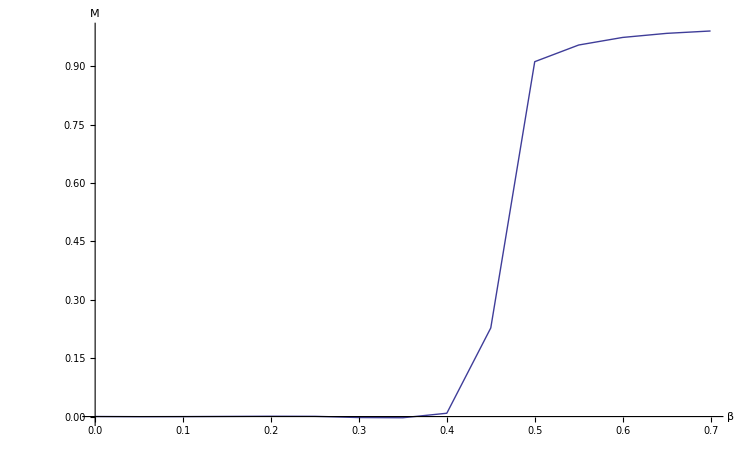

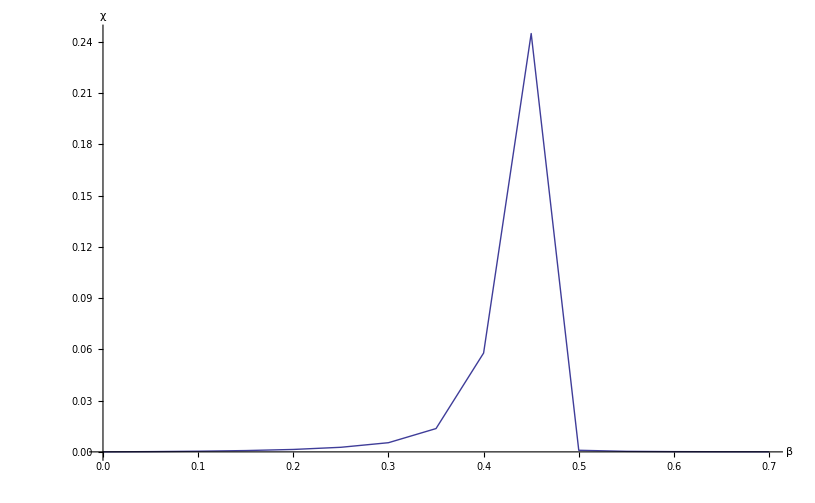

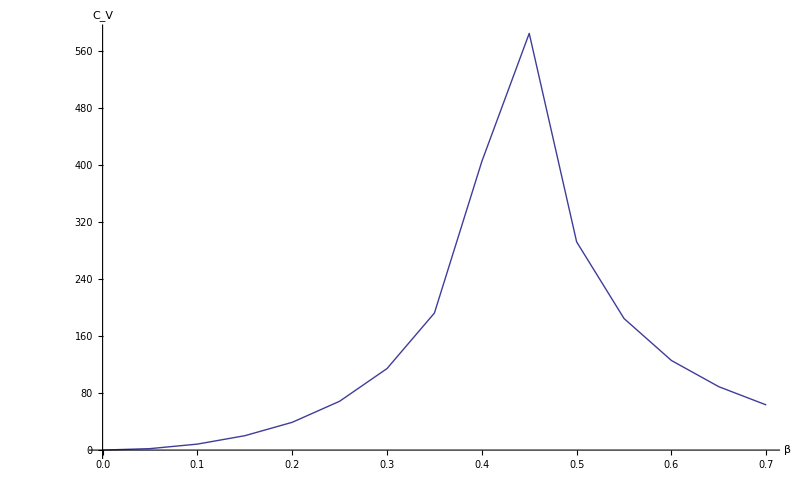

```mathematica
ListLinePlot[p1,PlotRange->All,AxesLabel->{β,M}]
ListLinePlot[p2,PlotRange->All,AxesLabel->{β,χ}]
ListLinePlot[p3,PlotRange->All,AxesLabel->{β,Subscript[C, V]}]
```

```mathematica
1/2.269//N
```

0.440723

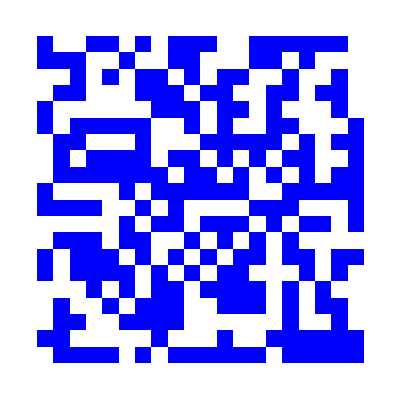
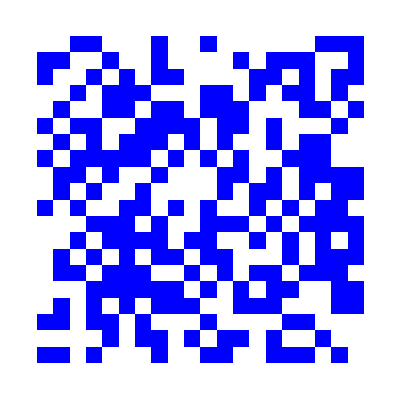
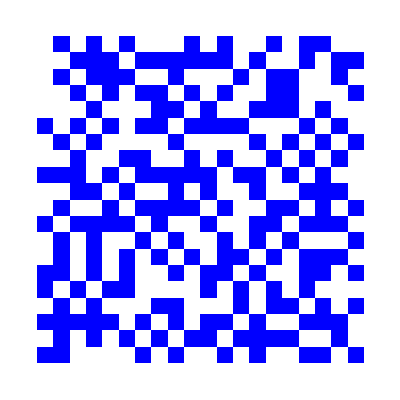
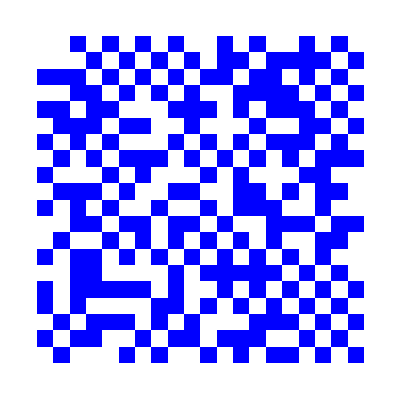
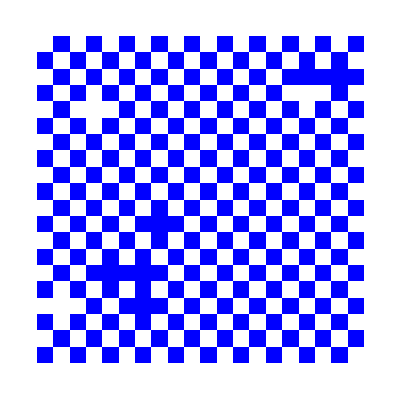
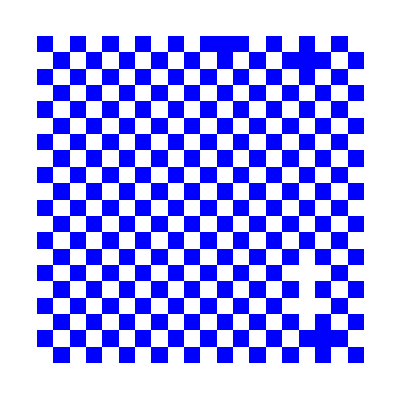
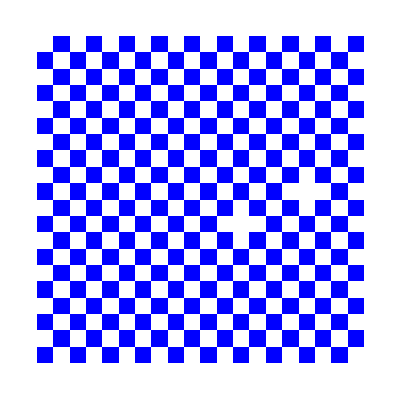

```mathematica
βs=Table[β,{β,0.1,0.7,0.1}];
simβvar=Parallelize[Table[mcSim[βs[[i]],-1,20,8111],{i,1,Dimensions[βs][[1]]}]];
Table[ArrayPlot[simβvar[[i*1,8111]],ColorRules->{1->Blue,-1->White}],{i,1,Dimensions[βs][[1]]}]
```

```mathematica
β=1;
j=1;
n=10;
iter=1000;
dauer=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer[[1]]
```

17.65402

```mathematica
com=Compile[{β,j,n,iter},mcSim[β,j,n,iter]];           (*bringt fast nichts*)
dauer1=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer1[[1]]
```

17.67202

```mathematica
ByteCount[dauer[[2]]]
```

29280080

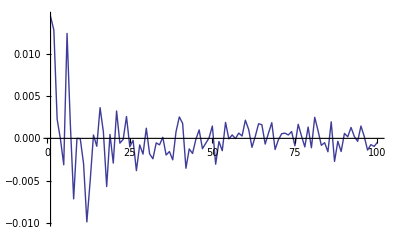

```mathematica
β=0;
j=1;
n=10;
maxiter=10000;
anzahl=100;
plt=Parallelize[Table[magnetization[mcSim[β,j,n,maxiter/anzahl*i],n],{i,1,anzahl}]];
ListLinePlot[plt,PlotRange->All]
```